```mathematica
(* Find an actual line that is perpendicular to the curve at a point with length 1.  its slope should be given by the normal ratio. *)
```

```mathematica
a = 2;
b = 1;
Clear[f,g,a,b]
f[t_]:={ a Cos[t], b Sin[t]}
g[t_]:=Assuming[t>0,FullSimplify[f[t]+f[t]/Norm[f[t]]]]
g1[t_]:=f[t][[2]]
ParametricPlot[{f[t],g[t]},{t,0,Pi/2},PlotRange->{{0,Max[a,b]+1},{0,Max[a,b]+1}},AspectRatio->1]
```

ParametricPlot::prng: Value of option PlotRange -> {{0, 1 + Max[a, b]}, {0, 1 + Max[a, b]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
D[Sqrt[Total[(f[t]-{x0,y0})^2]],t]
```

(-2 a (-x0+a Cos[t]) Sin[t]+2 b Cos[t] (-y0+b Sin[t]))/(2 √((-x0+a Cos[t])^2+(-y0+b Sin[t])^2))

```mathematica
Solve[%==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{«1»}

```mathematica
?EuclideanDistance
```

EuclideanDistance[u,v] gives the Euclidean distance between vectors u and v.

```mathematica
(* Do a cylinder method.  Integrate Pi r^2.  Integrate around the x-axis *)
```

```mathematica
(* first two fct1 and fct2 for chain rule *)
dfxdt=D[f[t][[1]],t];
dgxdt=D[g[t][[1]],t];
dfydt=D[f[t][[2]],t];
dgydt=D[g[t][[2]],t];


outside1=NIntegrate[Pi g[t][[2]]^2 Abs[dgxdt],{t,-Pi/2,Pi/2}];
inside1=NIntegrate[Pi (f[t][[2]])^2 Abs[dfxdt],{t,-Pi/2,Pi/2}];
outside2=NIntegrate[Pi g[t][[1]]^2 Abs[dgydt],{t,-Pi/2,Pi/2}];
inside2=NIntegrate[Pi (f[t][[1]])^2 Abs[dfydt],{t,-Pi/2,Pi/2}];
chocvol1=2(outside1-inside1)
chocvol2=2(outside2-inside2)
```

38.8749

69.3722

```mathematica
outside1
outside2
```

23.4356

35.222

```mathematica
N[4 Pi 3 3 1/3]
```

37.6991

```mathematica
inside1
inside2
```

8.37758

16.7552

```mathematica
N[28/3 Pi]
```

29.3215

```mathematica
outside1+outside2-inside1-inside2
```

46.0912

```mathematica
(* Try Again *)
```

```mathematica
a=3;b=1;

(* Check integration method *)
cv={a Cos[t],b Sin[t]};
int=cv[[1]]^2 D[cv[[2]],t];
in=Abs[2 Integrate[Pi int,{t,0,Pi/2}]];
cv2 = Assuming[t>0,Simplify[cv - D[cv,{t,2}]/Norm[D[cv,{t,2}]]]];
int2=cv2[[1]]^2 D[cv2[[2]],t];
out=Abs[2 NIntegrate[Pi Abs[int2],{t,0,Pi/2},PrecisionGoal->11,WorkingPrecision->11]];
trueinner = N[4/3 Pi a a b];
N[out-in,10]
```

76.90490557

```mathematica
in
```

16.7552

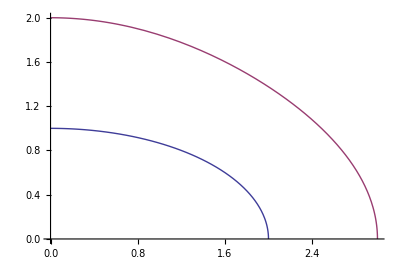

```mathematica
ParametricPlot[{cv,cv2},{t,0,Pi/2}]
```

```mathematica
a=2;b=1;

(* Check integration method *)
cv={Cos[t],3 Sin[t]};
norm={3 Cos[t],Sin[t]};
len=Sqrt[8 Cos[t]^2+1];
int=cv[[1]]^2 D[cv[[2]],t];
in=Abs[2 Integrate[Pi int,{t,0,Pi/2}]];
cv2 = Assuming[t>0,Simplify[cv + norm/len]];
int2=cv2[[1]]^2 D[cv2[[2]],t];
out=Abs[2 NIntegrate[Pi Abs[int2],{t,0,Pi/2},PrecisionGoal->11,WorkingPrecision->11]];
trueinner = N[4/3 Pi a a b];
N[out-in,10]
```

57.84790977

```mathematica
a=2;b=1;
cv = {a Cos[t],b Sin[t]};
outnorm=Assuming[{t>0&&a>0&&b>0},Simplify[{b Cos[t],a Sin[t]}/Sqrt[a^2 Sin[t]^2+b^2 Cos[t]^2]]];
cvout=cv+outnorm;
intgrd = cvout[[1]]^2 D[cvout[[2]],t];
outvol= 2 Pi NIntegrate[intgrd,{t,0,Pi/2}];
outvol-4/3 Pi a a
```

60.3548